```mathematica
ls=BinaryReadList["/tmp/mnist.out",{"Real64", "Real64"}];
```

```mathematica
label=BinaryReadList[NotebookDirectory[]<>"mnist.label.idx1" ,"Byte"][[9;;]];
```

```mathematica
labeledPts=Last/@#&/@GatherBy[Transpose[{label, ls}],First];
```

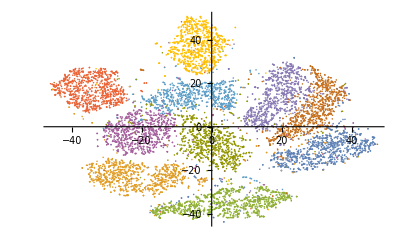

```mathematica
ListPlot[labeledPts]
```

```mathematica
28 * 28
```

784